```mathematica
P={Sin[θs]*Cos[ϕs],Sin[θs]*Sin[ϕs],Cos[θs]}; (*top polarization +1, along the direction of the spectator quark in the top rest frame*)
P=-P
uL={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
uT={Cos[θ]*Cos[ϕ],Cos[θ]*Sin[ϕ],-Sin[θ]};
uN={Sin[ϕ],-Cos[ϕ],0};

a0=1-(mW^2+2*mt*q)/mt^2; ?a0
a1=(mt^2/(2*mW^2))*(1-(mW^2-2*mt*q)/mt^2); ?a1
a2=(mt^2/(2*mW^2))*(1-(mW^2+2*mt*q)/mt^2); ?a2
a3=1-(mW^2-2*mt*q)/mt^2; ?a3
a4[ϕstar_]:=((mt/(Sqrt[2]*mW))*(1-(mW^2+2*mt*q)/mt^2))*Cos[ϕstar]; ?a4
a5=a4;
a6[ϕstar_]:=(mt/(Sqrt[2]*mW))*(1-(mW^2+2*mt*q)/mt^2)*(-Sin[ϕstar]); ?a6
a7=a6;
```

{-Cos[ϕs] Sin[θs],-Sin[θs] Sin[ϕs],-Cos[θs]}

Global`a0

a0=1-(mW^2+2 mt q)/mt^2

Global`a1

a1=(mt^2 (1-(mW^2-2 mt q)/mt^2))/(2 mW^2)

Global`a2

a2=(mt^2 (1-(mW^2+2 mt q)/mt^2))/(2 mW^2)

Global`a3

a3=1-(mW^2-2 mt q)/mt^2

Global`a4

a4[ϕstar_]:=((mt (1-(mW^2+2 mt q)/mt^2)) Cos[ϕstar])/(√2 mW)

Global`a6

a6[ϕstar_]:=(mt (1-(mW^2+2 mt q)/mt^2) (-Sin[ϕstar]))/(√2 mW)

```mathematica
(* CONSTRUCT THE FULLY DIFFERENTIAL CROSS SECTION, FUNCTION OF (θ,ϕ,θstar,ϕstar) *)

Prob[θ_,ϕ_,θstar_,ϕstar_] :=( Abs[a0]^2*(1+λ *Cos[θstar])^2 + 2*Abs[a1]^2*Sin[θstar]^2)*(1+P.uL)+
    (2*Abs[a2]^2*Sin[θstar]^2+Abs[a3]^2*(1-λ *Cos[θstar])^2)*(1-P.uL) +
      λ*2 *Sqrt[2]*(a4[ϕstar]*(1+λ *Cos[θstar])+
a5[ϕstar]*(1-λ *Cos[θstar]))*Sin[θstar]*P.uT+
      λ*2 *Sqrt[2]*(a6[ϕstar]*(1+λ *Cos[θstar])+
a7[ϕstar]*(1-λ *Cos[θstar]))*Sin[θstar]*P.uN
Prob[θ,ϕ,θstar,ϕstar] 
Clear[λ];Simplify[Prob[θ,ϕ,θstar,ϕstar]]
```

2 √2 λ (0.466802 (1-λ Cos[θstar]) Cos[ϕstar]+0.466802 (1+λ Cos[θstar]) Cos[ϕstar]) Sin[θstar] (0.59379 Cos[θ] Cos[ϕ]+0.453596 Sin[θ]-0.664578 Cos[θ] Sin[ϕ])+(0.0979109 (1+λ Cos[θstar])^2+15.1766 Sin[θstar]^2) (1-0.453596 Cos[θ]+0.59379 Cos[ϕ] Sin[θ]-0.664578 Sin[θ] Sin[ϕ])+(1.53206 (1-λ Cos[θstar])^2+0.969907 Sin[θstar]^2) (1+0.453596 Cos[θ]-0.59379 Cos[ϕ] Sin[θ]+0.664578 Sin[θ] Sin[ϕ])+2 √2 λ Sin[θstar] (0.+0.664578 Cos[ϕ]+0.59379 Sin[ϕ]) (-0.466802 (1-λ Cos[θstar]) Sin[ϕstar]-0.466802 (1+λ Cos[θstar]) Sin[ϕstar])

1.19778 λ Cos[ϕstar] Sin[θstar] (1. Sin[θ]+Cos[θ] (1.30907 Cos[ϕ]-1.46513 Sin[ϕ]))+(0.0979109 (1+λ Cos[θstar])^2+15.1766 Sin[θstar]^2) (1-0.453596 Cos[θ]+0.59379 Cos[ϕ] Sin[θ]-0.664578 Sin[θ] Sin[ϕ])+(1.53206 (-1.+λ Cos[θstar])^2+0.969907 Sin[θstar]^2) (1+0.453596 Cos[θ]-0.59379 Cos[ϕ] Sin[θ]+0.664578 Sin[θ] Sin[ϕ])-1.75491 λ Sin[θstar] (1. Cos[ϕ]+0.893484 Sin[ϕ]) Sin[ϕstar]

```mathematica
Clear[λ]; λ=1; (* +1 for top quark and -1 for anti-top quark*)
ProbTop=Simplify[Prob[θ,ϕ,θstar,ϕstar]]
```

1.19778 Cos[ϕstar] Sin[θstar] (1. Sin[θ]+Cos[θ] (1.30907 Cos[ϕ]-1.46513 Sin[ϕ]))+(0.0979109 (1+Cos[θstar])^2+15.1766 Sin[θstar]^2) (1-0.453596 Cos[θ]+0.59379 Cos[ϕ] Sin[θ]-0.664578 Sin[θ] Sin[ϕ])+(1.53206 (-1.+Cos[θstar])^2+0.969907 Sin[θstar]^2) (1+0.453596 Cos[θ]-0.59379 Cos[ϕ] Sin[θ]+0.664578 Sin[θ] Sin[ϕ])-1.75491 Sin[θstar] (1. Cos[ϕ]+0.893484 Sin[ϕ]) Sin[ϕstar]

```mathematica
1/(2 mt mW)(8 (mt^2-mW^2-2 mt q) Cos[ϕstar] (Cos[θs] Sin[θ]-Cos[θ] Cos[ϕ-ϕs] Sin[θs]) Sin[θstar]-mt mW (8 Abs[1-(mW^2+2 mt q)/mt^2]^2 Cos[θstar/2]^4+Abs[(mt^2-mW^2+2 mt q)/mW^2]^2 Sin[θstar]^2) (-1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs])+mt mW (8 Abs[1-(mW^2-2 mt q)/mt^2]^2 Sin[θstar/2]^4+Abs[(mt^2-mW^2-2 mt q)/mW^2]^2 Sin[θstar]^2) (1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs])+8 (mt^2-mW^2-2 mt q) Sin[θs] Sin[θstar] Sin[ϕ-ϕs] Sin[ϕstar])
```

1/(2 mt mW)(8 (mt^2-mW^2-2 mt q) Cos[ϕstar] (Cos[θs] Sin[θ]-Cos[θ] Cos[ϕ-ϕs] Sin[θs]) Sin[θstar]-mt mW (8 Abs[1-(mW^2+2 mt q)/mt^2]^2 Cos[θstar/2]^4+Abs[(mt^2-mW^2+2 mt q)/mW^2]^2 Sin[θstar]^2) (-1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs])+mt mW (8 Abs[1-(mW^2-2 mt q)/mt^2]^2 Sin[θstar/2]^4+Abs[(mt^2-mW^2-2 mt q)/mW^2]^2 Sin[θstar]^2) (1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs])+8 (mt^2-mW^2-2 mt q) Sin[θs] Sin[θstar] Sin[ϕ-ϕs] Sin[ϕstar])

```mathematica
Clear[λ]; λ=-1; (* +1 for top quark and -1 for anti-top quark*)
ProbAntitop=Simplify[Prob[θ,ϕ,θstar,ϕstar]]
```

-1.19778 Cos[ϕstar] Sin[θstar] (1. Sin[θ]+Cos[θ] (1.30907 Cos[ϕ]-1.46513 Sin[ϕ]))+(0.0979109 (-1.+Cos[θstar])^2+15.1766 Sin[θstar]^2) (1-0.453596 Cos[θ]+0.59379 Cos[ϕ] Sin[θ]-0.664578 Sin[θ] Sin[ϕ])+(1.53206 (1+Cos[θstar])^2+0.969907 Sin[θstar]^2) (1+0.453596 Cos[θ]-0.59379 Cos[ϕ] Sin[θ]+0.664578 Sin[θ] Sin[ϕ])+1.75491 Sin[θstar] (1. Cos[ϕ]+0.893484 Sin[ϕ]) Sin[ϕstar]

207.621-44.3394 Cos[θ]+58.0435 Cos[ϕ] Sin[θ]-64.9631 Sin[θ] Sin[ϕ]

-Graphics3D-

1304.52-278.593 Cos[θ]

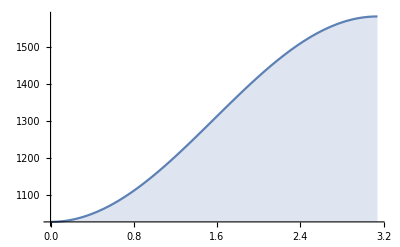

32.1743-56.6178 Cos[θstar]+32.1743 Cos[θstar]^2+15.0518 Cos[ϕstar] Sin[θstar]+318.719 Sin[θstar]^2

-Graphics3D-

202.157-355.74 Cos[θstar]+202.157 Cos[θstar]^2+2002.57 Sin[θstar]^2

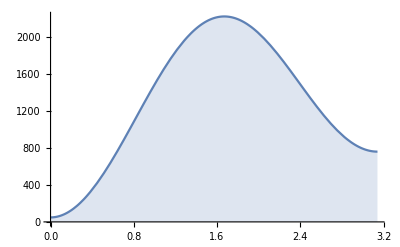

652.26+30.1035 Cos[ϕstar]

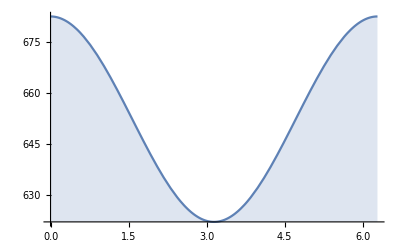

207.621-44.3394 Cos[θ]+58.0435 Cos[ϕ] Sin[θ]-64.9631 Sin[θ] Sin[ϕ]

-Graphics3D-

1304.52-278.593 Cos[θ]

-Graphics-

32.1743+56.6178 Cos[θstar]+32.1743 Cos[θstar]^2-15.0518 Cos[ϕstar] Sin[θstar]+318.719 Sin[θstar]^2

-Graphics3D-

202.157+355.74 Cos[θstar]+202.157 Cos[θstar]^2+2002.57 Sin[θstar]^2

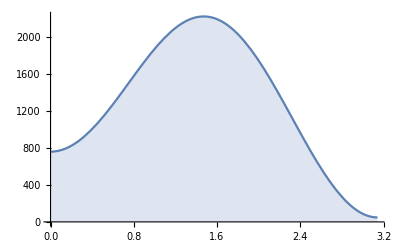

```mathematica
(* PLOTTING TOP AND ANTITOP DISTRIBUTIONS *)
Clear[mW]; mW=82.;
Clear[mt]; mt=173.;
Clear[q]; q=40;
Clear[θs]; θs=1.1;
Clear[ϕs]; ϕs=2.3;
Integrate[ProbTop,{θstar,0,Pi},{ϕstar,0,2Pi}]
Plot3D[%,{θ,0,Pi},{ϕ,0,2Pi}]
Integrate[ProbTop,{θstar,0,Pi},{ϕstar,0,2Pi},{ϕ,0,2Pi}]
Plot[%,{θ,0,Pi},Filling->Axis]

Integrate[ProbTop,{θ,0,Pi},{ϕ,0,2Pi}]
Plot3D[%,{θstar,0,Pi},{ϕstar,0,2Pi}]
Integrate[ProbTop,{θ,0,Pi},{ϕ,0,2Pi},{ϕstar,0,2Pi}]
Plot[%,{θstar,0,Pi},Filling->Axis]

Integrate[ProbTop,{θ,0,Pi},{ϕ,0,2Pi},{θstar,0,Pi}]
Plot[%,{ϕstar,0,2Pi},Filling->Axis]

Integrate[ProbAntitop,{θstar,0,Pi},{ϕstar,0,2Pi}]
Plot3D[%,{θ,0,Pi},{ϕ,0,2Pi}]
Integrate[ProbAntitop,{θstar,0,Pi},{ϕstar,0,2Pi},{ϕ,0,2Pi}]
Plot[%,{θ,0,Pi},Filling->Axis]

Integrate[ProbAntitop,{θ,0,Pi},{ϕ,0,2Pi}]
Plot3D[%,{θstar,0,Pi},{ϕstar,0,2Pi}]
Integrate[ProbAntitop,{θ,0,Pi},{ϕ,0,2Pi},{ϕstar,0,2Pi}]
Plot[%,{θstar,0,Pi},Filling->Axis]
```

```mathematica
ProbTop===ProbAntitop
```

False

```mathematica
Simplify[ProbTop-ProbAntitop]
```

4 Abs[1-(mW^2-2 mt q)/mt^2]^2 Cos[θstar] (-1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs])+4 Abs[1-(mW^2+2 mt q)/mt^2]^2 Cos[θstar] (1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs])-(8 (mt^2-mW^2-2 mt q) Sin[θstar] (Cos[θs] Cos[ϕstar] Sin[θ]+Sin[θs] (-Cos[θ] Cos[ϕ-ϕs] Cos[ϕstar]+Sin[ϕ-ϕs] Sin[ϕstar])))/(mt mW)

```mathematica
(* SOME TESTS.......SPLITTING THE PROBABILITY FOR SIMPLIFICATIONS *)
Clear[λ];
ProbSplit=Level[Prob[θ,ϕ,θstar,ϕstar],1]
```

{2 √2 λ ((mt (1-(mW^2+2 mt q)/mt^2) (1-λ Cos[θstar]) Cos[ϕstar])/(√2 mW)+(mt (1-(mW^2+2 mt q)/mt^2) (1+λ Cos[θstar]) Cos[ϕstar])/(√2 mW)) Sin[θstar] (-Cos[θs] Sin[θ]+Cos[θ] Cos[ϕ] Cos[ϕs] Sin[θs]+Cos[θ] Sin[θs] Sin[ϕ] Sin[ϕs]),(Abs[1-(mW^2-2 mt q)/mt^2]^2 (1-λ Cos[θstar])^2+1/2 Abs[(mt^2 (1-(mW^2+2 mt q)/mt^2))/mW^2]^2 Sin[θstar]^2) (1-Cos[θ] Cos[θs]-Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]-Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs]),(Abs[1-(mW^2+2 mt q)/mt^2]^2 (1+λ Cos[θstar])^2+1/2 Abs[(mt^2 (1-(mW^2-2 mt q)/mt^2))/mW^2]^2 Sin[θstar]^2) (1+Cos[θ] Cos[θs]+Cos[ϕ] Cos[ϕs] Sin[θ] Sin[θs]+Sin[θ] Sin[θs] Sin[ϕ] Sin[ϕs]),2 √2 λ Sin[θstar] (Cos[ϕs] Sin[θs] Sin[ϕ]-Cos[ϕ] Sin[θs] Sin[ϕs]) (-(mt (1-(mW^2+2 mt q)/mt^2) (1-λ Cos[θstar]) Sin[ϕstar])/(√2 mW)-(mt (1-(mW^2+2 mt q)/mt^2) (1+λ Cos[θstar]) Sin[ϕstar])/(√2 mW))}

```mathematica
NewProb=Simplify[Sum[FullSimplify[Part[ProbSplit,i]],{i,Length[ProbSplit]}]]
```

1/2 ((8 (mt^2-mW^2-2 mt q) λ Cos[ϕstar] (-Cos[θs] Sin[θ]+Cos[θ] Cos[ϕ-ϕs] Sin[θs]) Sin[θstar])/(mt mW)-(-1+Cos[θ] Cos[θs]+Cos[ϕ-ϕs] Sin[θ] Sin[θs]) (2 Abs[1-(mW^2-2 mt q)/mt^2]^2 (-1+λ Cos[θstar])^2+Abs[(mt^2-mW^2-2 mt q)/mW^2]^2 Sin[θstar]^2)+(1+Cos[θ] Cos[θs]+Cos[ϕ-ϕs] Sin[θ] Sin[θs]) (2 Abs[1-(mW^2+2 mt q)/mt^2]^2 (1+λ Cos[θstar])^2+Abs[(mt^2-mW^2+2 mt q)/mW^2]^2 Sin[θstar]^2)+(8 (-mt^2+mW^2+2 mt q) λ Sin[θs] Sin[θstar] Sin[ϕ-ϕs] Sin[ϕstar])/(mt mW))

```mathematica
(* SOME TESTS.......CHECK IF/WHEN THE PDF TURNS NEGATIVE!!!!!!! *)


Reduce[{ProbTop<0},{θ,ϕ}]
```

$Aborted